```mathematica
Hold[1/(4 g (t+2))(4 t E0 expectedX[t - 1] + t (t - 1) (t - 2) expectedX[t - 3] - 4 (t + 1) expectedX[t + 1])] /. t -> u - 3
```

Hold[(4 (-3+u) E0 expectedX[(-3+u)-1]+(-3+u) ((-3+u)-1) ((-3+u)-2) expectedX[(-3+u)-3]-4 ((-3+u)+1) expectedX[(-3+u)+1])/(4 g ((-3+u)+2))]

```mathematica
expectedX[0] := 1;
expectedX[2] := x2;
expectedX[4] := 1/(3g)(E0 - 2 x2);
expectedX[u_?EvenQ] := (4 (-3+u) E0 expectedX[(-3+u)-1]+(-3+u) ((-3+u)-1) ((-3+u)-2) expectedX[(-3+u)-3]-4 ((-3+u)+1) expectedX[(-3+u)+1])/(4 g ((-3+u)+2));
expectedX[_?OddQ] := 0;
```

```mathematica
expectedX[6]
```

(6-(16 (E0-2 x2))/(3 g)+12 E0 x2)/(20 g)

```mathematica
matPositive[K_] := Table[expectedX[i + j], {i, 0, K}, {j, 0, K}];
```

```mathematica
region = Reduce[Det[FullSimplify[matPositive[8] /. g -> 1]] ≥ 0, {E0, x2}];
```

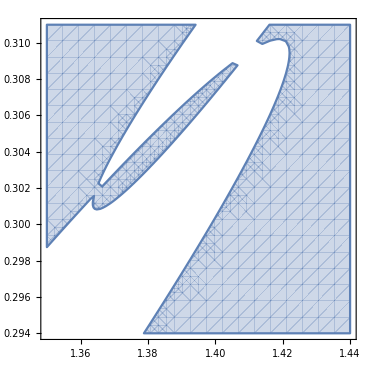

```mathematica
RegionPlot[region, {E0, 1.35, 1.44}, {x2, 0.294, 0.311}]
```

以上条件是不够的；完整的对半正定性的判断需要计算本征值。

```mathematica
region = Reduce[Det[FullSimplify[matPositive[6] /. g -> 1]] ≥ 0, {E0, x2}];
```

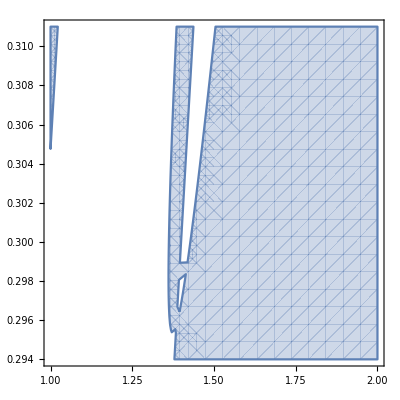

```mathematica
RegionPlot[region, {E0, 1, 2}, {x2, 0.294, 0.311}]
```

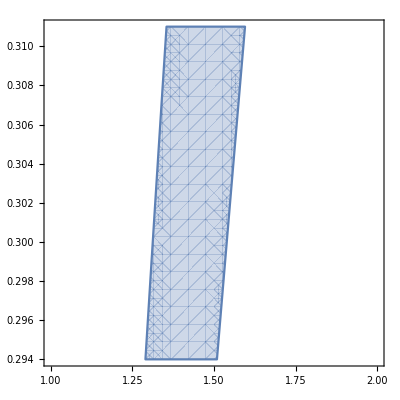

```mathematica
region = Reduce[Det[FullSimplify[matPositive[4] /. g -> 1]] ≥ 0, {E0, x2}];
RegionPlot[region, {E0, 1, 2}, {x2, 0.294, 0.311}]
```